## Non-Autonomous System BSA, 2024

```mathematica
ClearAll["Global`*"]
```

### Initial Data № 7.4

```mathematica
X = {x[1][t], x[2][t], x[3][t]};
P = {{a, Sin[2 * t], 0}, {Cos[2 * t], -a, -Sin[t]}, {0, Cos[t], -1}};
Eq = Thread[D[X, t] == P . X];
```

```mathematica
Print[TableForm[Eq] /. {x[i_] :> Subscript[x, i]}]
```

x_1'[t]==a x_1[t]+Sin[2 t] x_2[t]
x_2'[t]==Cos[2 t] x_1[t]-a x_2[t]-Sin[t] x_3[t]
x_3'[t]==Cos[t] x_2[t]-x_3[t]

```mathematica
Print[MatrixForm[D[X, t] /. {x[i_] :> Subscript[x, i]}], " = ", MatrixForm[P], " x ", MatrixForm[X /. {x[i_] :> Subscript[x, i]}]]
```

(x_1'[t]
x_2'[t]
x_3'[t]) = (a | Sin[2 t] | 0
Cos[2 t] | -a | -Sin[t]
0 | Cos[t] | -1) x (x_1[t]
x_2[t]
x_3[t])

### Compute Eigenvalues

```mathematica
T = 2 * Pi;
```

```mathematica
NA = Transpose[X /. Table[NDSolve[Union[Eq /. a -> #, Thread[(X /. t -> 0) == UnitVector[3, i]]], X, {t, 0, T}][[1]], {i, 3}]] /. {t -> T} &;
NI = Eigenvalues[NA[#]] &;
NIAbs = Abs[NI[#]] &;
```

```mathematica
LExp = N[Exp[Integrate[Tr[P] /. {a -> #}, {t, 0, T}]]] &;
LI = ρ /. NSolve[ρ^3 + LExp[#] * (-ρ^2 + ρ - 1), ρ] &;
LIAbs = Abs[LI[#]] &;
```

```mathematica
NExp = Apply[Times, NIAbs[#]] &;
```

### Stability Domain

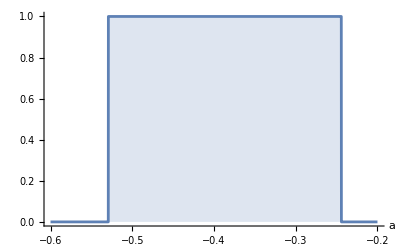

```mathematica
Plot[If[Max[NIAbs[a]] < 1, 1, 0], {a, -0.6, -0.2}, AxesLabel -> {a, None}, Filling -> Axis, FillingStyle -> Automatic]
```

#### Left Border

```mathematica
Round[NIAbs[-0.5292], 0.001]
```

{1.,0.15,0.012}

#### Right Border

```mathematica
Round[NIAbs[-0.2442], 0.001]
```

{1.,0.085,0.022}

### Plot the Solution

```mathematica
PlotSolution[α_, τ_, i_] := (
	FX = X /. NDSolve[Union[Eq /. a -> α, Thread[(X /. t -> 0) == UnitVector[3, i]]], X, {t, 0, τ}][[1]];
	p1 = Plot[FX, {t, 0, τ}, PlotRange -> Full, PlotLegends -> Placed[{Subscript[x, 1], Subscript[x, 2], Subscript[x, 3]}, Bottom], 
		AxesLabel -> {t, x[t]}, GridLines -> Automatic, PlotStyle -> {Blue, Red, Darker[Green]}, 
		PlotLabel->Style[Round[NI[α], 0.001], 10], ImageSize->Scaled[0.9]];
	p2 = Show[Plot[If[Max[NIAbs[a]] < 1, 1, 0], {a, -0.6, -0.2}, AxesLabel -> {a, None}, Filling -> Axis, AspectRatio->1],
		Graphics[{Red, PointSize[Large], Point[{α, 0.5}]}], ImageSize -> Scaled[0.7]];
	GraphicsRow[{p1, p2}]
);
```

```mathematica
Manipulate[PlotSolution[a, 100, i], {a, -0.6, -0.2, Appearance -> "Open"}, {i, {1, 2, 3}}]
```

### Check with Liouville Formula

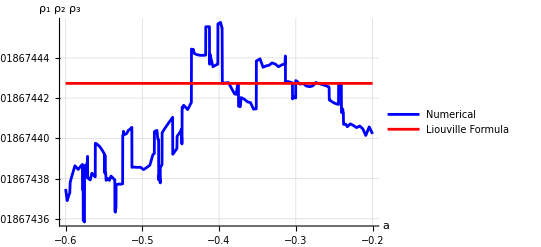

```mathematica
Plot[{NExp[a], LExp[a]}, {a, -0.6, -0.2}, PlotRange -> Full, PlotLegends -> Placed[{"Numerical", "Liouville Formula"}, Bottom], 
		AxesLabel -> {a, Subscript[ρ, 1] * Subscript[ρ, 2] * Subscript[ρ, 3]}, GridLines -> Automatic, PlotStyle -> {Blue, Red}]
```